```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin active addresses: bitinfocharts.com.

- Bitcoin market capitalization: bitinfocharts.com.

- Bitcoin hourly price: Recent (2023/2024) data - bitstamp.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2023 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
firstPrice="2018-05-15";
lastPriceDate="2024-08-10";
```

```mathematica
(* Compute recent (2023/24) Log market cap data: *)
(* Slow. Pre-processed below for performance *)
priceSource = "Bitcoin_price-"<>StringDelete[firstPrice, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv"
```

Bitcoin_price-20180515-20240810.csv

```mathematica
prices =Import[base<>priceSource, HeaderLines->1]
```

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[closingPricesFilter, First]
```

```mathematica
Length[hourlyPrices]
```

54715

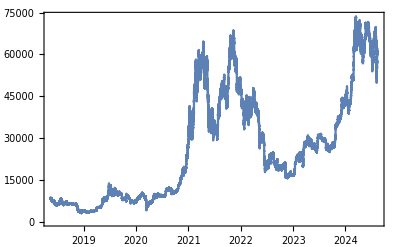

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"Bitcoin_price-hourly-"<>StringDelete[firstPrice, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/Bitcoin_price-hourly-20180515-20240810.csv

```mathematica
(* Prices list. Pre-processed for performance: *)
hourlyPricesList = Import[base<>"Bitcoin_price-hourly-"<>StringDelete[firstPrice, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv"]
```

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data *)
supplyJson = Import[base<>"Bitcoin_circulating_supply-"<>"20090110"<>"-"<>StringDelete[lastPriceDate, "-"]<>".json"];
supplyTs=supplyJson[[3]][[2]][[All, 1]][[All,2]]/1000;
supplyQuantity=supplyJson[[3]][[2]][[All, 2]][[All,2]];
```

```mathematica
supplyTimestamps=MapThread[{#1, #2}&,{supplyTs, supplyQuantity}];
```

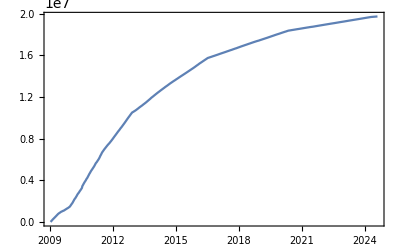

```mathematica
DateListPlot[supplyTimestamps,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Block[{},Off[ InterpolatingFunction::dmval];Interpolation[supplyTimestamps]]
```

InterpolatingFunction[…]

```mathematica
{supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}
```

{1231568277,1723223109}

```mathematica
{hourlyPricesList[[1]][[1]],hourlyPricesList[[-1]][[1]]}
```

{1526364000,1723334400}

```mathematica
{supplyFunction[hourlyPricesList[[1]][[1]]], supplyFunction[hourlyPricesList[[-3]][[1]]]}
```

{1.70341×10^7,1.97382×10^7}

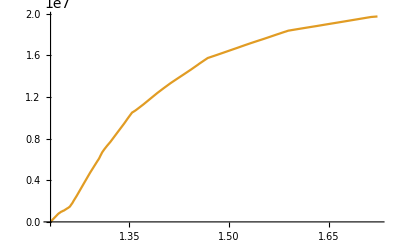

```mathematica
Plot[{,supplyFunction[i]}, {i, supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}]
```

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPricesList
```

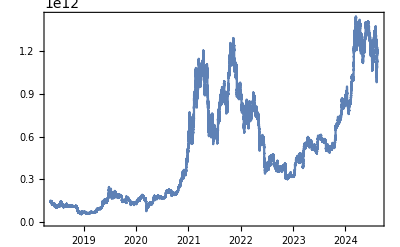

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2023/2024 bubble turning point: *)
(* Generalized to multiple bubbles *)
 (*bubblesDate={{"2019-11-25", "2021-02-15"}, {"2023-08-14", lastPriceDate}} *)
```

```mathematica
(* bubblesDate={{"2019-11-25", "2021-02-15"}, {"2022-11-10", lastPriceDate}} *)
```

```mathematica
(*bubblesDate={{"2019-11-25", "2021-02-15"}, {"2023-01-01", lastPriceDate}} *)
bubblesDate={{"2019-11-25", "2021-02-15"}, {"2023-01-01", "2024-04-01"}}
```

{{2019-11-25,2021-02-15},{2023-01-01,2024-04-01}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1574632800,1613340000},{1672524000,1711922400}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{448,456}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1574632800,25.5671},{1672524000,26.4845}}

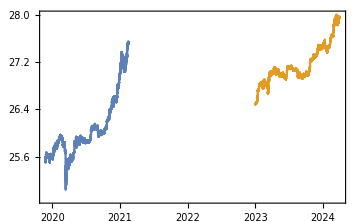

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.00093,0.997022},{1.0403,0.97654}}

```mathematica
Length/@bubblesScaled
```

{10753,10945}

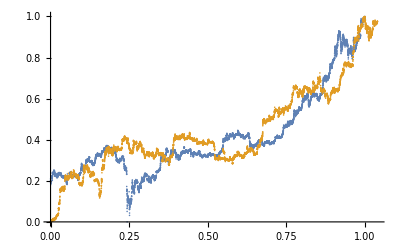

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
bubble=2
bubbleScaled=bubblesScaled[[bubble]];
Export[base<>"bubbleScaled.tsv", Join[{{"time","value"}},bubbleScaled]]
```

2

/Users/mauro/Projects/Bitcoin/bubbleScaled.tsv

```mathematica
(* Shortcut: *)
bestBandwidth=1250 ;(* Manual. So that it rejects the larger windows. *)
bestSpan=bestBandwidth/Length[bubbleScaled]//N
```

0.114207

```mathematica
bestBandwidth=.
bestSpan=0.15
estimatedNParams = 10.5(* From R. Only valid for the 2nd bubble *)
effectiveDfs=11243.18
```

0.15

10.5

11243.2

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
(* maxDist=Max[bubbleScaled[[All, 1]]]-Min[bubbleScaled[[All, 1]]]; *)
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

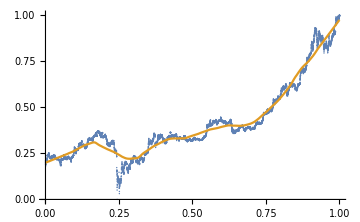
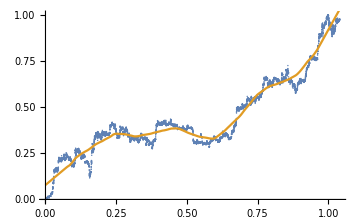

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}]
```

```mathematica
bubblesScaled[[bubble]]//Length
```

10945

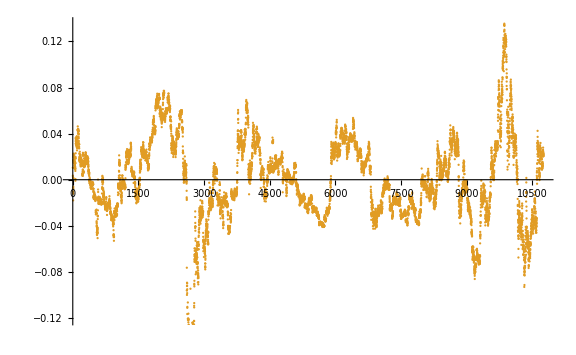
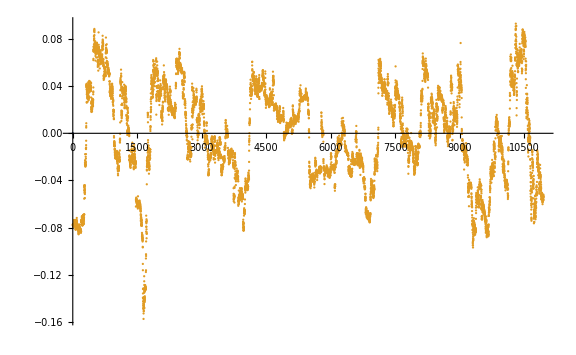

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0372846,0.0407056}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}]
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{14.9677,18.1564}

```mathematica
(* Larger than in R) *)
```

```mathematica
(* Residual Standard Error: *)
ℛsSE=√(Total[#^2]/(Length[#]-estimatedNParams))&/@ℛs
```

{0.0373272,0.0407489}

```mathematica
ℛsSE=√(Total[#^2]/effectiveDfs)&/@ℛs
```

{0.0364866,0.0401856}

```mathematica
(* Slightly larger than in R) *)
```

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Use the second bubble: *)
bubble=2;
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Profiling over 0.1 < m < 0.9, 5 < ω < 15 and 1. < tc < 3 months in the future *)
minM=0.1;
maxM=1;
minω=5;
maxω=15;
months=1;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
maxTc=(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.06579

```mathematica
(* Define 14 days resolution scaled interval step: *)
stepTc=14/bubblesDays[[bubble]]//N
```

0.0307018

```mathematica
(* Define 10 days resolution scaled initial time step *)
stepTi=10/bubblesDays[[bubble]]//N
```

0.0219298

```mathematica
(* Slow. Shortcut below *)
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

{409.331,{{a→0.968089,b→-0.85376,c→-0.00891314,d→-0.147259,T_1→0.,tc→1.0404,m→0.6,ω→5.9,RSS→31.0224,ℛerror→0.0028362,ℛσ→0.0532414,LL→47312.6,ρ→0.99814,σ→-0.00324526,μ→-5.05394×10^-19},{a→0.964757,b→-0.846036,c→-0.00526139,d→-0.142901,T_1→0.0219298,tc→1.0404,m→0.6,ω→5.9,RSS→30.3166,ℛerror→0.00283147,ℛσ→0.0531967,LL→46212.3,ρ→0.998083,σ→-0.00329177,μ→1.34016×10^-18},{a→0.936886,b→-0.873263,c→0.068443,d→-0.170345,T_1→0.0438596,tc→1.0404,m→0.7,ω→5.,RSS→25.674,ℛerror→0.00245075,ℛσ→0.0494908,LL→45294.2,ρ→0.997846,σ→-0.00324663,μ→-1.01955×10^-18},{a→0.997646,b→-0.812991,c→-0.00446313,d→-0.0237199,T_1→0.0657895,tc→1.0404,m→0.5,ω→12.,RSS→54.835,ℛerror→0.00535237,ℛσ→0.0731385,LL→44320.7,ρ→0.999016,σ→-0.00324314,μ→-1.60358×10^-19},{a→0.996171,b→-0.915923,c→0.047218,d→-0.158696,T_1→0.0877193,tc→1.0404,m→0.6,ω→5.,RSS→21.1343,ℛerror→0.00211027,ℛσ→0.0459239,LL→43298.4,ρ→0.997505,σ→-0.00324218,μ→7.96989×10^-20},{a→0.998863,b→-0.815505,c→-0.00735348,d→-0.02502,T_1→0.109649,tc→1.0404,m→0.5,ω→12.1,RSS→54.3012,ℛerror→0.00555,ℛσ→0.0744755,LL→42341.1,ρ→0.999059,σ→-0.00323081,μ→2.24895×10^-19},{a→0.948325,b→-0.905034,c→0.0486378,d→-0.185856,T_1→0.131579,tc→1.0404,m→0.7,ω→5.,RSS→22.9231,ℛerror→0.00239957,ℛσ→0.04897,LL→41328.6,ρ→0.997829,σ→-0.00322458,μ→-7.61813×10^-19},{a→0.935809,b→-0.878194,c→-0.0425622,d→-0.182216,T_1→0.153509,tc→1.0404,m→0.7,ω→5.9,RSS→27.0119,ℛerror→0.00289734,ℛσ→0.0538096,LL→40329.4,ρ→0.998177,σ→-0.00324756,μ→-6.96631×10^-19},{a→0.991729,b→-0.90424,c→0.0558544,d→-0.157678,T_1→0.175439,tc→1.0404,m→0.6,ω→5.,RSS→18.5549,ℛerror→0.00204079,ℛσ→0.0451602,LL→39610.8,ρ→0.997576,σ→-0.0031421,μ→2.63745×10^-18},{a→0.947098,b→-0.901699,c→0.0509378,d→-0.183627,T_1→0.197368,tc→1.0404,m→0.7,ω→5.,RSS→20.5494,ℛerror→0.00231908,ℛσ→0.0481406,LL→38754.7,ρ→0.997934,σ→-0.00309261,μ→1.46959×10^-18},{a→0.950656,b→-0.912619,c→0.0422341,d→-0.183215,T_1→0.219298,tc→1.0404,m→0.7,ω→5.,RSS→19.9369,ℛerror→0.00231018,ℛσ→0.0480477,LL→37748.6,ρ→0.997906,σ→-0.00310723,μ→-1.65608×10^-19},{a→1.0032,b→-0.935292,c→0.0334578,d→-0.154832,T_1→0.241228,tc→1.0404,m→0.6,ω→5.,RSS→16.59,ℛerror→0.001975,ℛσ→0.0444251,LL→36670.1,ρ→0.99736,σ→-0.00322575,μ→-1.32358×10^-18},{a→0.95949,b→-0.940461,c→0.0206732,d→-0.177993,T_1→0.263158,tc→1.0404,m→0.7,ω→5.,RSS→17.8868,ℛerror→0.0021896,ℛσ→0.0467759,LL→35673.7,ρ→0.997768,σ→-0.00312314,μ→-2.58805×10^-19},{a→0.963668,b→-0.954039,c→0.0109538,d→-0.173211,T_1→0.285088,tc→1.0404,m→0.7,ω→5.,RSS→17.1619,ℛerror→0.002162,ℛσ→0.0464797,LL→34806.5,ρ→0.99774,σ→-0.00312261,μ→1.56358×10^-18},{a→0.965135,b→-0.958875,c→0.00767818,d→-0.171167,T_1→0.307018,tc→1.0404,m→0.7,ω→5.,RSS→16.9557,ℛerror→0.00219975,ℛσ→0.0468832,LL→33793.9,ρ→0.997904,σ→-0.00303349,μ→-1.37084×10^-18},{a→0.978507,b→-1.01501,c→-0.179808,d→-0.031095,T_1→0.328947,tc→1.0404,m→0.7,ω→6.7,RSS→13.0897,ℛerror→0.00175066,ℛσ→0.0418241,LL→32725.8,ρ→0.99732,σ→-0.00305957,μ→-4.96972×10^-19},{a→0.980912,b→-1.02294,c→-0.178875,d→-0.0247635,T_1→0.350877,tc→1.0404,m→0.7,ω→6.7,RSS→12.8539,ℛerror→0.00177393,ℛσ→0.0421006,LL→31647.5,ρ→0.997304,σ→-0.00308934,μ→-1.01774×10^-18},{a→0.980159,b→-1.02096,c→-0.181558,d→-0.0126306,T_1→0.372807,tc→1.0404,m→0.7,ω→6.8,RSS→12.8249,ℛerror→0.00182795,ℛσ→0.0427362,LL→30636.2,ρ→0.997355,σ→-0.00310608,μ→-1.85351×10^-18},{a→0.976793,b→-1.00883,c→-0.1844,d→-0.03472,T_1→0.394737,tc→1.0404,m→0.7,ω→6.7,RSS→12.225,ℛerror→0.00180177,ℛσ→0.0424285,LL→29632.8,ρ→0.997333,σ→-0.00309668,μ→6.14087×10^-19},{a→0.980025,b→-1.02026,c→-0.177728,d→-0.0283705,T_1→0.416667,tc→1.0404,m→0.7,ω→6.7,RSS→11.9106,ℛerror→0.0018173,ℛσ→0.0426104,LL→28601.8,ρ→0.997299,σ→-0.00312924,μ→7.70859×10^-19},{a→0.983579,b→-1.03313,c→-0.168766,d→-0.0231454,T_1→0.438596,tc→1.0404,m→0.7,ω→6.7,RSS→11.5547,ℛerror→0.00182741,ℛσ→0.0427279,LL→27531.5,ρ→0.997237,σ→-0.00317398,μ→4.29064×10^-19},{a→0.988734,b→-1.05253,c→-0.156665,d→-0.00477715,T_1→0.460526,tc→1.0404,m→0.7,ω→6.8,RSS→11.2025,ℛerror→0.00183859,ℛσ→0.0428577,LL→26475.1,ρ→0.997219,σ→-0.00319404,μ→-2.90831×10^-19},{a→0.992215,b→-1.06579,c→-0.145989,d→-0.00517977,T_1→0.482456,tc→1.0404,m→0.7,ω→6.8,RSS→10.908,ℛerror→0.00186081,ℛσ→0.043115,LL→25385.3,ρ→0.997161,σ→-0.00324623,μ→1.19761×10^-18},{a→0.99681,b→-1.08381,c→-0.132207,d→-0.00973678,T_1→0.504386,tc→1.0404,m→0.7,ω→6.8,RSS→10.4268,ℛerror→0.00185168,ℛσ→0.0430082,LL→24301.,ρ→0.996947,σ→-0.00335788,μ→-1.02542×10^-18}}}

```mathematica
(* Shortcut: *)
fits= {409.331298,{{a->0.9680892742295686,b->-0.8537595001878492,c->-0.008913140693958094,d->-0.1472586799676855,Subscript[T, 1]->0.,tc->1.0404041825095056,m->0.6,ω->5.9,RSS->31.022355410448114,ℛerror->0.0028361999826703337,ℛσ->0.053241384734708935,LL->47312.585230805635,ρ->0.9981404214452613,σ->-0.003245262032826061,μ->-5.053942972168586*^-19},{a->0.9647573643387082,b->-0.8460364459596483,c->-0.005261386823398949,d->-0.14290059018410883,Subscript[T, 1]->0.021929824561403508,tc->1.0404041825095056,m->0.6,ω->5.9,RSS->30.31655703263624,ℛerror->0.002831470723137783,ℛσ->0.053196662576097196,LL->46212.341720016426,ρ->0.9980834620987062,σ->-0.0032917711662725914,μ->1.3401626490689828*^-18},{a->0.9368863402937252,b->-0.8732631444385391,c->0.06844303356488914,d->-0.170344823546386,Subscript[T, 1]->0.043859649122807015,tc->1.0404041825095056,m->0.7000000000000001,ω->5.,RSS->25.67400870373986,ℛerror->0.00245074538981862,ℛσ->0.04949083308077172,LL->45294.16941332647,ρ->0.997845756490783,σ->-0.003246627204716298,μ->-1.019554287836339*^-18},{a->0.9976460123723065,b->-0.8129905820639144,c->-0.00446312735350008,d->-0.023719933211359644,Subscript[T, 1]->0.06578947368421052,tc->1.0404041825095056,m->0.5,ω->12.,RSS->54.83504969109025,ℛerror->0.005352371858573963,ℛσ->0.07313849238595187,LL->44320.65050098176,ρ->0.9990162944283572,σ->-0.003243138938793159,μ->-1.6035770242712811*^-19},{a->0.9961705677193459,b->-0.9159230463496549,c->0.04721795430919506,d->-0.1586960885665059,Subscript[T, 1]->0.08771929824561403,tc->1.0404041825095056,m->0.6,ω->5.,RSS->21.134317858897976,ℛerror->0.0021102663863103318,ℛσ->0.045923881367346604,LL->43298.35363881126,ρ->0.9975045317491534,σ->-0.0032421778116518154,μ->7.969893583858699*^-20},{a->0.9988631625130996,b->-0.8155051267431511,c->-0.007353479716814143,d->-0.025019967250118895,Subscript[T, 1]->0.10964912280701754,tc->1.0404041825095056,m->0.5,ω->12.100000000000001,RSS->54.30124132880044,ℛerror->0.005550004224121058,ℛσ->0.07447551806803059,LL->42341.08954166479,ρ->0.9990585136169188,σ->-0.003230807841551808,μ->2.2489474219156675*^-19},{a->0.9483248651422556,b->-0.9050338398280875,c->0.04863783107646833,d->-0.1858561309151912,Subscript[T, 1]->0.13157894736842105,tc->1.0404041825095056,m->0.7000000000000001,ω->5.,RSS->22.923075187520855,ℛerror->0.0023995682181012093,ℛσ->0.04897001179696614,LL->41328.601658736414,ρ->0.9978294352479528,σ->-0.003224579362793154,μ->-7.618128342983523*^-19},{a->0.9358087536952453,b->-0.8781941455317154,c->-0.04256215331377937,d->-0.18221624023899013,Subscript[T, 1]->0.15350877192982454,tc->1.0404041825095056,m->0.7000000000000001,ω->5.9,RSS->27.01191026326857,ℛerror->0.0028973410129002008,ℛσ->0.05380964199254173,LL->40329.422634298746,ρ->0.9981769158112551,σ->-0.0032475598104629365,μ->-6.966307900783709*^-19},{a->0.9917287985539144,b->-0.9042402371776908,c->0.0558544385999536,d->-0.15767841318798836,Subscript[T, 1]->0.17543859649122806,tc->1.0404041825095056,m->0.6,ω->5.,RSS->18.554865608465487,ℛerror->0.0020407903220925525,ℛσ->0.04516020870478788,LL->39610.846438586166,ρ->0.9975763422080399,σ->-0.0031420957612664025,μ->2.6374519160680442*^-18},{a->0.9470978773500671,b->-0.9016990384034186,c->0.05093783154571224,d->-0.18362737304574728,Subscript[T, 1]->0.19736842105263158,tc->1.0404041825095056,m->0.7000000000000001,ω->5.,RSS->20.549407155562488,ℛerror->0.0023190844324074583,ℛσ->0.04814057733499518,LL->38754.69819870789,ρ->0.9979341705291763,σ->-0.0030926062413733964,μ->1.4695877726674818*^-18},{a->0.9506562628509317,b->-0.9126191884308116,c->0.042234105011308865,d->-0.18321538255171402,Subscript[T, 1]->0.21929824561403508,tc->1.0404041825095056,m->0.7000000000000001,ω->5.,RSS->19.936882285765247,ℛerror->0.002310183347133864,ℛσ->0.048047667061680455,LL->37748.58033190817,ρ->0.9979064856518299,σ->-0.003107225066329838,μ->-1.65607783216559*^-19},{a->1.0032018454463616,b->-0.9352922992009927,c->0.03345778871527488,d->-0.15483216715024556,Subscript[T, 1]->0.24122807017543857,tc->1.0404041825095056,m->0.6,ω->5.,RSS->16.589993139138528,ℛerror->0.001974999183230777,ℛσ->0.044425099622419265,LL->36670.111923423436,ρ->0.9973600294872467,σ->-0.0032257469465634377,μ->-1.3235844694512385*^-18},{a->0.959490306317022,b->-0.940460804400589,c->0.020673226063462384,d->-0.17799279807896604,Subscript[T, 1]->0.2631578947368421,tc->1.0404041825095056,m->0.7000000000000001,ω->5.,RSS->17.886813532759703,ℛerror->0.0021895964662455264,ℛσ->0.04677594919365664,LL->35673.743162226,ρ->0.9977682480525359,σ->-0.0031231407917388506,μ->-2.5880528465226974*^-19},{a->0.96366822885876,b->-0.9540392577126082,c->0.010953817621329895,d->-0.1732111536671509,Subscript[T, 1]->0.2850877192982456,tc->1.0404041825095056,m->0.7000000000000001,ω->5.,RSS->17.16191970236863,ℛerror->0.002161995427358104,ℛσ->0.04647969987315083,LL->34806.51904327562,ρ->0.9977404416198051,σ->-0.003122606763895383,μ->1.5635815275525407*^-18},{a->0.9651353953318044,b->-0.958875356700975,c->0.007678183459411609,d->-0.17116719093932586,Subscript[T, 1]->0.3070175438596491,tc->1.0404041825095056,m->0.7000000000000001,ω->5.,RSS->16.955652387267378,ℛerror->0.0021997473258001266,ℛσ->0.04688322032288148,LL->33793.86893058948,ρ->0.9979042842026035,σ->-0.00303349176025202,μ->-1.3708449881928292*^-18},{a->0.9785070286260107,b->-1.015007337744388,c->-0.1798078454661213,d->-0.0310950284512565,Subscript[T, 1]->0.3289473684210526,tc->1.0404041825095056,m->0.7000000000000001,ω->6.7,RSS->13.08970452660722,ℛerror->0.0017506626356302284,ℛσ->0.04182414283371325,LL->32725.84229546049,ρ->0.997320361567135,σ->-0.0030595671969294415,μ->-4.969722550178516*^-19},{a->0.9809119747034412,b->-1.0229393242289326,c->-0.1788754756496686,d->-0.024763516047502366,Subscript[T, 1]->0.3508771929824561,tc->1.0404041825095056,m->0.7000000000000001,ω->6.7,RSS->12.853912596780155,ℛerror->0.0017739321828291687,ℛσ->0.042100647333492246,LL->31647.45676563264,ρ->0.9973036939482888,σ->-0.00308933836938327,μ->-1.0177408333058487*^-18},{a->0.9801589124415232,b->-1.0209605625637008,c->-0.1815575748632669,d->-0.012630641963543193,Subscript[T, 1]->0.37280701754385964,tc->1.0404041825095056,m->0.7000000000000001,ω->6.8,RSS->12.82488846254179,ℛerror->0.0018279487546382254,ℛσ->0.04273624749860811,LL->30636.15422192271,ρ->0.9973549176497257,σ->-0.0031060803388339125,μ->-1.8535107054735543*^-18},{a->0.9767928213171391,b->-1.0088324322454727,c->-0.1843995144130501,d->-0.03471996123261133,Subscript[T, 1]->0.39473684210526316,tc->1.0404041825095056,m->0.7000000000000001,ω->6.7,RSS->12.225006851091948,ℛerror->0.0018017696169627042,ℛσ->0.04242850119095122,LL->29632.826831463666,ρ->0.9973325794578177,σ->-0.0030966823279984196,μ->6.140872216583949*^-19},{a->0.9800247571226158,b->-1.0202572687575153,c->-0.17772841496473316,d->-0.028370479379811516,Subscript[T, 1]->0.41666666666666663,tc->1.0404041825095056,m->0.7000000000000001,ω->6.7,RSS->11.910614743620966,ℛerror->0.001817304660302253,ℛσ->0.04261035662143231,LL->28601.82446388254,ρ->0.9972993339146176,σ->-0.003129241589909012,μ->7.708585167879204*^-19},{a->0.9835789701099292,b->-1.033130669102082,c->-0.1687658255254367,d->-0.023145365849551434,Subscript[T, 1]->0.43859649122807015,tc->1.0404041825095056,m->0.7000000000000001,ω->6.7,RSS->11.554695249177149,ℛerror->0.0018274071246524037,ℛσ->0.0427279148978136,LL->27531.481770126935,ρ->0.9972367209910259,σ->-0.0031739825368269636,μ->4.2906364903779485*^-19},{a->0.988734032169182,b->-1.0525310715680203,c->-0.15666534420792239,d->-0.004777148965940712,Subscript[T, 1]->0.4605263157894737,tc->1.0404041825095056,m->0.7000000000000001,ω->6.8,RSS->11.202518202344695,ℛerror->0.0018385882491949277,ℛσ->0.042857665652964595,LL->26475.069452904725,ρ->0.997218556546252,σ->-0.0031940434922881,μ->-2.90830977548076*^-19},{a->0.9922149808531833,b->-1.0657899253529188,c->-0.145989057301465,d->-0.005179773467646637,Subscript[T, 1]->0.48245614035087714,tc->1.0404041825095056,m->0.7000000000000001,ω->6.8,RSS->10.908044395015558,ℛerror->0.001860805935690133,ℛσ->0.04311500053501358,LL->25385.323594378402,ρ->0.997161013085805,σ->-0.003246232555034244,μ->1.1976071331419485*^-18},{a->0.9968099737151934,b->-1.083806774166105,c->-0.13220703792191288,d->-0.009736777304312712,Subscript[T, 1]->0.5043859649122807,tc->1.0404041825095056,m->0.7000000000000001,ω->6.8,RSS->10.426806398570314,ℛerror->0.0018516793462209757,ℛσ->0.043008236725240845,LL->24301.018387074924,ρ->0.9969469178869906,σ->-0.0033578834805982087,μ->-1.0254177492040942*^-18}}}
```

{409.331,{{a→0.968089,b→-0.85376,c→-0.00891314,d→-0.147259,T_1→0.,tc→1.0404,m→0.6,ω→5.9,RSS→31.0224,ℛerror→0.0028362,ℛσ→0.0532414,LL→47312.6,ρ→0.99814,σ→-0.00324526,μ→-5.05394×10^-19},{a→0.964757,b→-0.846036,c→-0.00526139,d→-0.142901,T_1→0.0219298,tc→1.0404,m→0.6,ω→5.9,RSS→30.3166,ℛerror→0.00283147,ℛσ→0.0531967,LL→46212.3,ρ→0.998083,σ→-0.00329177,μ→1.34016×10^-18},{a→0.936886,b→-0.873263,c→0.068443,d→-0.170345,T_1→0.0438596,tc→1.0404,m→0.7,ω→5.,RSS→25.674,ℛerror→0.00245075,ℛσ→0.0494908,LL→45294.2,ρ→0.997846,σ→-0.00324663,μ→-1.01955×10^-18},{a→0.997646,b→-0.812991,c→-0.00446313,d→-0.0237199,T_1→0.0657895,tc→1.0404,m→0.5,ω→12.,RSS→54.835,ℛerror→0.00535237,ℛσ→0.0731385,LL→44320.7,ρ→0.999016,σ→-0.00324314,μ→-1.60358×10^-19},{a→0.996171,b→-0.915923,c→0.047218,d→-0.158696,T_1→0.0877193,tc→1.0404,m→0.6,ω→5.,RSS→21.1343,ℛerror→0.00211027,ℛσ→0.0459239,LL→43298.4,ρ→0.997505,σ→-0.00324218,μ→7.96989×10^-20},{a→0.998863,b→-0.815505,c→-0.00735348,d→-0.02502,T_1→0.109649,tc→1.0404,m→0.5,ω→12.1,RSS→54.3012,ℛerror→0.00555,ℛσ→0.0744755,LL→42341.1,ρ→0.999059,σ→-0.00323081,μ→2.24895×10^-19},{a→0.948325,b→-0.905034,c→0.0486378,d→-0.185856,T_1→0.131579,tc→1.0404,m→0.7,ω→5.,RSS→22.9231,ℛerror→0.00239957,ℛσ→0.04897,LL→41328.6,ρ→0.997829,σ→-0.00322458,μ→-7.61813×10^-19},{a→0.935809,b→-0.878194,c→-0.0425622,d→-0.182216,T_1→0.153509,tc→1.0404,m→0.7,ω→5.9,RSS→27.0119,ℛerror→0.00289734,ℛσ→0.0538096,LL→40329.4,ρ→0.998177,σ→-0.00324756,μ→-6.96631×10^-19},{a→0.991729,b→-0.90424,c→0.0558544,d→-0.157678,T_1→0.175439,tc→1.0404,m→0.6,ω→5.,RSS→18.5549,ℛerror→0.00204079,ℛσ→0.0451602,LL→39610.8,ρ→0.997576,σ→-0.0031421,μ→2.63745×10^-18},{a→0.947098,b→-0.901699,c→0.0509378,d→-0.183627,T_1→0.197368,tc→1.0404,m→0.7,ω→5.,RSS→20.5494,ℛerror→0.00231908,ℛσ→0.0481406,LL→38754.7,ρ→0.997934,σ→-0.00309261,μ→1.46959×10^-18},{a→0.950656,b→-0.912619,c→0.0422341,d→-0.183215,T_1→0.219298,tc→1.0404,m→0.7,ω→5.,RSS→19.9369,ℛerror→0.00231018,ℛσ→0.0480477,LL→37748.6,ρ→0.997906,σ→-0.00310723,μ→-1.65608×10^-19},{a→1.0032,b→-0.935292,c→0.0334578,d→-0.154832,T_1→0.241228,tc→1.0404,m→0.6,ω→5.,RSS→16.59,ℛerror→0.001975,ℛσ→0.0444251,LL→36670.1,ρ→0.99736,σ→-0.00322575,μ→-1.32358×10^-18},{a→0.95949,b→-0.940461,c→0.0206732,d→-0.177993,T_1→0.263158,tc→1.0404,m→0.7,ω→5.,RSS→17.8868,ℛerror→0.0021896,ℛσ→0.0467759,LL→35673.7,ρ→0.997768,σ→-0.00312314,μ→-2.58805×10^-19},{a→0.963668,b→-0.954039,c→0.0109538,d→-0.173211,T_1→0.285088,tc→1.0404,m→0.7,ω→5.,RSS→17.1619,ℛerror→0.002162,ℛσ→0.0464797,LL→34806.5,ρ→0.99774,σ→-0.00312261,μ→1.56358×10^-18},{a→0.965135,b→-0.958875,c→0.00767818,d→-0.171167,T_1→0.307018,tc→1.0404,m→0.7,ω→5.,RSS→16.9557,ℛerror→0.00219975,ℛσ→0.0468832,LL→33793.9,ρ→0.997904,σ→-0.00303349,μ→-1.37084×10^-18},{a→0.978507,b→-1.01501,c→-0.179808,d→-0.031095,T_1→0.328947,tc→1.0404,m→0.7,ω→6.7,RSS→13.0897,ℛerror→0.00175066,ℛσ→0.0418241,LL→32725.8,ρ→0.99732,σ→-0.00305957,μ→-4.96972×10^-19},{a→0.980912,b→-1.02294,c→-0.178875,d→-0.0247635,T_1→0.350877,tc→1.0404,m→0.7,ω→6.7,RSS→12.8539,ℛerror→0.00177393,ℛσ→0.0421006,LL→31647.5,ρ→0.997304,σ→-0.00308934,μ→-1.01774×10^-18},{a→0.980159,b→-1.02096,c→-0.181558,d→-0.0126306,T_1→0.372807,tc→1.0404,m→0.7,ω→6.8,RSS→12.8249,ℛerror→0.00182795,ℛσ→0.0427362,LL→30636.2,ρ→0.997355,σ→-0.00310608,μ→-1.85351×10^-18},{a→0.976793,b→-1.00883,c→-0.1844,d→-0.03472,T_1→0.394737,tc→1.0404,m→0.7,ω→6.7,RSS→12.225,ℛerror→0.00180177,ℛσ→0.0424285,LL→29632.8,ρ→0.997333,σ→-0.00309668,μ→6.14087×10^-19},{a→0.980025,b→-1.02026,c→-0.177728,d→-0.0283705,T_1→0.416667,tc→1.0404,m→0.7,ω→6.7,RSS→11.9106,ℛerror→0.0018173,ℛσ→0.0426104,LL→28601.8,ρ→0.997299,σ→-0.00312924,μ→7.70859×10^-19},{a→0.983579,b→-1.03313,c→-0.168766,d→-0.0231454,T_1→0.438596,tc→1.0404,m→0.7,ω→6.7,RSS→11.5547,ℛerror→0.00182741,ℛσ→0.0427279,LL→27531.5,ρ→0.997237,σ→-0.00317398,μ→4.29064×10^-19},{a→0.988734,b→-1.05253,c→-0.156665,d→-0.00477715,T_1→0.460526,tc→1.0404,m→0.7,ω→6.8,RSS→11.2025,ℛerror→0.00183859,ℛσ→0.0428577,LL→26475.1,ρ→0.997219,σ→-0.00319404,μ→-2.90831×10^-19},{a→0.992215,b→-1.06579,c→-0.145989,d→-0.00517977,T_1→0.482456,tc→1.0404,m→0.7,ω→6.8,RSS→10.908,ℛerror→0.00186081,ℛσ→0.043115,LL→25385.3,ρ→0.997161,σ→-0.00324623,μ→1.19761×10^-18},{a→0.99681,b→-1.08381,c→-0.132207,d→-0.00973678,T_1→0.504386,tc→1.0404,m→0.7,ω→6.8,RSS→10.4268,ℛerror→0.00185168,ℛσ→0.0430082,LL→24301.,ρ→0.996947,σ→-0.00335788,μ→-1.02542×10^-18}}}

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

6.82219

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.0404 | ℛσ→0.0532414 | LL→47312.6
T_1→0.0219298 | tc→1.0404 | ℛσ→0.0531967 | LL→46212.3
T_1→0.0438596 | tc→1.0404 | ℛσ→0.0494908 | LL→45294.2
T_1→0.0657895 | tc→1.0404 | ℛσ→0.0731385 | LL→44320.7
T_1→0.0877193 | tc→1.0404 | ℛσ→0.0459239 | LL→43298.4
T_1→0.109649 | tc→1.0404 | ℛσ→0.0744755 | LL→42341.1
T_1→0.131579 | tc→1.0404 | ℛσ→0.04897 | LL→41328.6
T_1→0.153509 | tc→1.0404 | ℛσ→0.0538096 | LL→40329.4
T_1→0.175439 | tc→1.0404 | ℛσ→0.0451602 | LL→39610.8
T_1→0.197368 | tc→1.0404 | ℛσ→0.0481406 | LL→38754.7
T_1→0.219298 | tc→1.0404 | ℛσ→0.0480477 | LL→37748.6
T_1→0.241228 | tc→1.0404 | ℛσ→0.0444251 | LL→36670.1
T_1→0.263158 | tc→1.0404 | ℛσ→0.0467759 | LL→35673.7
T_1→0.285088 | tc→1.0404 | ℛσ→0.0464797 | LL→34806.5
T_1→0.307018 | tc→1.0404 | ℛσ→0.0468832 | LL→33793.9
T_1→0.328947 | tc→1.0404 | ℛσ→0.0418241 | LL→32725.8
T_1→0.350877 | tc→1.0404 | ℛσ→0.0421006 | LL→31647.5
T_1→0.372807 | tc→1.0404 | ℛσ→0.0427362 | LL→30636.2
T_1→0.394737 | tc→1.0404 | ℛσ→0.0424285 | LL→29632.8
T_1→0.416667 | tc→1.0404 | ℛσ→0.0426104 | LL→28601.8
T_1→0.438596 | tc→1.0404 | ℛσ→0.0427279 | LL→27531.5
T_1→0.460526 | tc→1.0404 | ℛσ→0.0428577 | LL→26475.1
T_1→0.482456 | tc→1.0404 | ℛσ→0.043115 | LL→25385.3
T_1→0.504386 | tc→1.0404 | ℛσ→0.0430082 | LL→24301.

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.0404

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.0404

1.0404

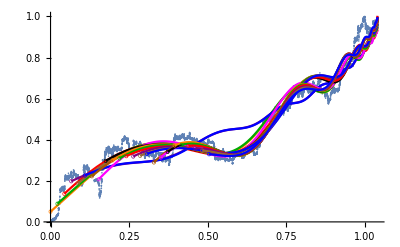

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* Rejection criteria: See if the (standardized) residuals of the fits (ℛerror field divided by ℛσ) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0219298,0.0438596,0.0657895,0.0877193,0.109649,0.131579,0.153509,0.175439,0.197368,0.219298,0.241228,0.263158,0.285088,0.307018,0.328947,0.350877,0.372807,0.394737,0.416667,0.438596,0.460526,0.482456,0.504386}

{0.0028362,0.00283147,0.00245075,0.00535237,0.00211027,0.00555,0.00239957,0.00289734,0.00204079,0.00231908,0.00231018,0.001975,0.0021896,0.002162,0.00219975,0.00175066,0.00177393,0.00182795,0.00180177,0.0018173,0.00182741,0.00183859,0.00186081,0.00185168}

{31.0224,30.3166,25.674,54.835,21.1343,54.3012,22.9231,27.0119,18.5549,20.5494,19.9369,16.59,17.8868,17.1619,16.9557,13.0897,12.8539,12.8249,12.225,11.9106,11.5547,11.2025,10.908,10.4268}

{0.0532414,0.0531967,0.0494908,0.0731385,0.0459239,0.0744755,0.04897,0.0538096,0.0451602,0.0481406,0.0480477,0.0444251,0.0467759,0.0464797,0.0468832,0.0418241,0.0421006,0.0427362,0.0424285,0.0426104,0.0427279,0.0428577,0.043115,0.0430082}

```mathematica
Export[base<>"t1s.tsv", Join[{{"t1"}},T1s]]
```

/Users/mauro/Projects/Bitcoin/t1s.tsv

```mathematica
(* Only bubble 2 *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

10945

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
bubble
```

2

```mathematica
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}]
```

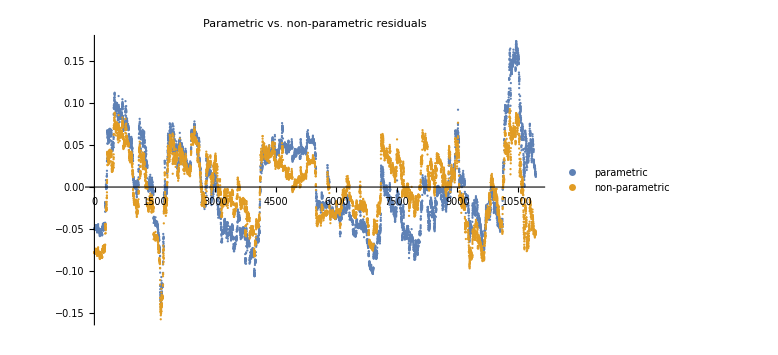

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{18.1564,31.0224}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0401856,0.053256}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.00161488,0.0028362}

```mathematica
selN=Length[T1s];
selN
```

24

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}]
```

```mathematica
Length/@selNpBestFit
```

{10945,10705,10465,10225,9985,9745,9505,9265,9025,8785,8545,8305,8065,7825,7585,7345,7105,6865,6625,6385,6145,5905,5665,5425}

```mathematica
selBubbleScaled=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;,2]], {i,1,selN}]
```

```mathematica
Length/@selBubbleScaled
```

{10945,10705,10465,10225,9985,9745,9505,9265,9025,8785,8545,8305,8065,7825,7585,7345,7105,6865,6625,6385,6145,5905,5665,5425}

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{10945,10705,10465,10225,9985,9745,9505,9265,9025,8785,8545,8305,8065,7825,7585,7345,7105,6865,6625,6385,6145,5905,5665,5425}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.0028362,0.00283147,0.00245075,0.00535237,0.00211027,0.00555,0.00239957,0.00289734,0.00204079,0.00231908,0.00231018,0.001975,0.0021896,0.002162,0.00219975,0.00175066,0.00177393,0.00182795,0.00180177,0.0018173,0.00182741,0.00183859,0.00186081,0.00185168}

```mathematica
RSSs
```

{31.0224,30.3166,25.674,54.835,21.1343,54.3012,22.9231,27.0119,18.5549,20.5494,19.9369,16.59,17.8868,17.1619,16.9557,13.0897,12.8539,12.8249,12.225,11.9106,11.5547,11.2025,10.908,10.4268}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0407056,0.0394852,0.0394798,0.0384919,0.0381859,0.0384032,0.0387336,0.0368365,0.0362028,0.0361006,0.0362647,0.0356593,0.0359666,0.0363135,0.0368104,0.0373041,0.0376245,0.0370047,0.0368615,0.0367103,0.0368826,0.0375053,0.0380776,0.0381619}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.996658,σ→-0.00332475,μ→-4.82831×10^-6},{ρ→0.996398,σ→-0.0033482,μ→9.87493×10^-7},{ρ→0.996456,σ→-0.00332049,μ→2.36187×10^-7},{ρ→0.996368,σ→-0.00327742,μ→-5.58784×10^-6},{ρ→0.996365,σ→-0.00325283,μ→-9.66532×10^-6},{ρ→0.996392,σ→-0.00325893,μ→-0.0000100164},{ρ→0.996466,σ→-0.00325332,μ→-9.84275×10^-6},{ρ→0.995456,σ→-0.00350763,μ→-3.88643×10^-6},{ρ→0.996105,σ→-0.00319195,μ→-2.96401×10^-6},{ρ→0.996218,σ→-0.00313644,μ→-6.73738×10^-6},{ρ→0.996188,σ→-0.00316323,μ→-9.77866×10^-6},{ρ→0.996166,σ→-0.0031194,μ→-0.0000153734},{ρ→0.996284,σ→-0.00309756,μ→-0.0000160227},{ρ→0.996427,σ→-0.00306677,μ→-0.0000172637},{ρ→0.996469,σ→-0.00309045,μ→-0.0000158944},{ρ→0.996492,σ→-0.00312172,μ→-0.0000146409},{ρ→0.996465,σ→-0.00316056,μ→-0.0000120569},{ρ→0.996297,σ→-0.00318116,μ→-6.11141×10^-6},{ρ→0.996257,σ→-0.00318622,μ→-0.0000106488},{ρ→0.996206,σ→-0.0031947,μ→-0.0000163923},{ρ→0.996204,σ→-0.00321052,μ→-0.0000208773},{ρ→0.996232,σ→-0.00325247,μ→-0.0000227135},{ρ→0.996147,σ→-0.00333907,μ→-0.0000262163},{ρ→0.996142,σ→-0.00334849,μ→-0.0000312129}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[-4.82831×10^-6,{0.996658},0.000011054],ARProcess[9.87493×10^-7,{0.996398},0.0000112104],ARProcess[2.36187×10^-7,{0.996456},0.0000110257],ARProcess[-5.58784×10^-6,{0.996368},0.0000107415],ARProcess[-9.66532×10^-6,{0.996365},0.0000105809],ARProcess[-0.0000100164,{0.996392},0.0000106206],ARProcess[-9.84275×10^-6,{0.996466},0.0000105841],ARProcess[-3.88643×10^-6,{0.995456},0.0000123035],ARProcess[-2.96401×10^-6,{0.996105},0.0000101886],ARProcess[-6.73738×10^-6,{0.996218},9.83724×10^-6],ARProcess[-9.77866×10^-6,{0.996188},0.000010006],ARProcess[-0.0000153734,{0.996166},9.73068×10^-6],ARProcess[-0.0000160227,{0.996284},9.59489×10^-6],ARProcess[-0.0000172637,{0.996427},9.40507×10^-6],ARProcess[-0.0000158944,{0.996469},9.55087×10^-6],ARProcess[-0.0000146409,{0.996492},9.74515×10^-6],ARProcess[-0.0000120569,{0.996465},9.98914×10^-6],ARProcess[-6.11141×10^-6,{0.996297},0.0000101198],ARProcess[-0.0000106488,{0.996257},0.000010152],ARProcess[-0.0000163923,{0.996206},0.0000102061],ARProcess[-0.0000208773,{0.996204},0.0000103074],ARProcess[-0.0000227135,{0.996232},0.0000105786],ARProcess[-0.0000262163,{0.996147},0.0000111494],ARProcess[-0.0000312129,{0.996142},0.0000112124]}

{47308.7,46170.2,45234.7,44213.4,43149.4,42139.8,41090.,40038.6,39324.8,38419.7,37325.7,36259.9,35333.1,34303.2,33197.8,32075.2,30997.5,29933.2,28886.,27786.2,26685.8,25558.9,24430.3,23356.6}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
(* Allowing for the distribution of the residual standard error on different window sizes to be approximated by Monte Carlo. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

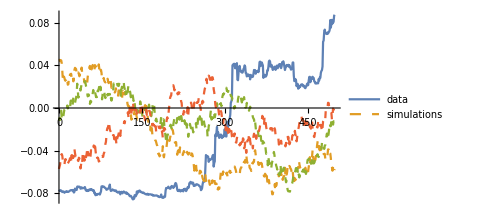
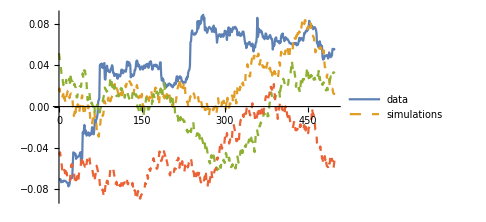
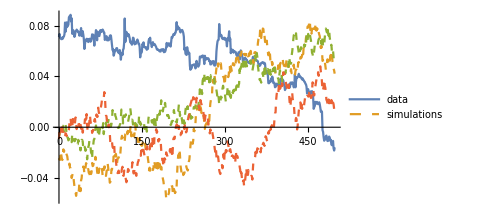
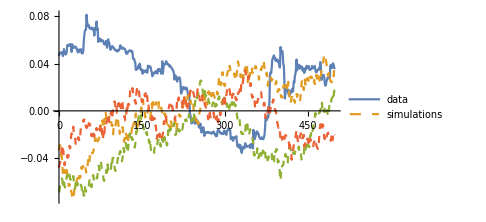
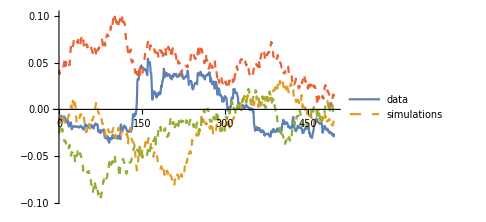
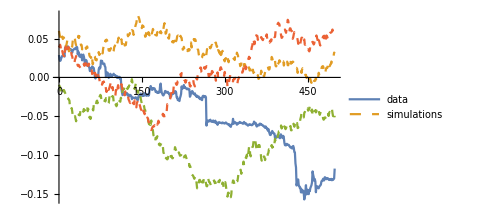
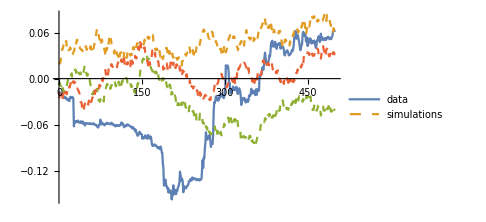
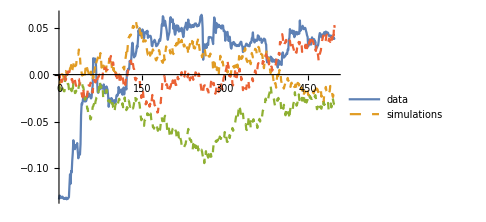

```mathematica
(* Show some simulations and data points *)
showPoints=500;
showSims=3;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* Characterize error variance *)
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess (TODO: List of effective dfs): *)
effectiveDfs
estimatedNParams
selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams 3, {i, selN}]
```

11243.2

10.5

{10913.5,10673.5,10433.5,10193.5,9953.5,9713.5,9473.5,9233.5,8993.5,8753.5,8513.5,8273.5,8033.5,7793.5,7553.5,7313.5,7073.5,6833.5,6593.5,6353.5,6113.5,5873.5,5633.5,5393.5}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEstimatedDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 20.5365 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 20.5366 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 3116432 Kb

Memory Used: 17.5647 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{7,2,18,0,54,0,22,0,17,4,11,40,16,28,38,190,182,111,143,129,137,184,199,218}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.007,0.002,0.018,0.,0.054,0.,0.022,0.,0.017,0.004,0.011,0.04,0.016,0.028,0.038,0.19,0.182,0.111,0.143,0.129,0.137,0.184,0.199,0.218}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False}

```mathematica
(* Take the largest that is not rejected *)
largestNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

5

```mathematica
selFit={fits[[largestNotRejectedIndex]], index-> largestNotRejectedIndex}//Flatten
```

{a→0.996171,b→-0.915923,c→0.047218,d→-0.158696,T_1→0.0877193,tc→1.0404,m→0.6,ω→5.,RSS→21.1343,ℛerror→0.00211027,ℛσ→0.0459239,LL→43298.4,ρ→0.997505,σ→-0.00324218,μ→7.96989×10^-20,index→5}

```mathematica
(* Use the fit is with smallest variance on the AR(1) as the best fit: *)
(* fit=MinimalBy[Table[{fits[[i]], index-> i}, {i,Length[fits]}], (#[[1]][[12]][[2]])^2&]//Flatten *)
(* bestIndex=fit//Last//Part[#,2]& *)
```

```mathematica
bestIndex=largestNotRejectedIndex
fit=fits[[bestIndex]]
```

5

{a→0.996171,b→-0.915923,c→0.047218,d→-0.158696,T_1→0.0877193,tc→1.0404,m→0.6,ω→5.,RSS→21.1343,ℛerror→0.00211027,ℛσ→0.0459239,LL→43298.4,ρ→0.997505,σ→-0.00324218,μ→7.96989×10^-20}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.6

5.

1.0404

43298.4

```mathematica
t1=Subscript[T, 1]/.fit
```

0.0877193

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

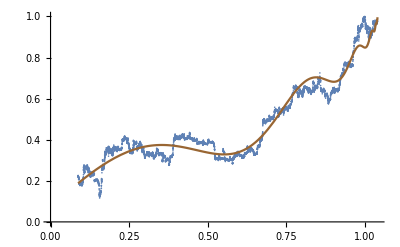

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→0.996171,b→-0.915923,c→0.047218,d→-0.158696,T_1→0.0877193,tc→1.0404,m→0.6,ω→5.,RSS→21.1343,ℛerror→0.00211027,ℛσ→0.0459239,LL→43298.4,ρ→0.997505,σ→-0.00324218,μ→7.96989×10^-20}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.997505,σ→-0.00324218,μ→4.64427×10^-20}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

LessEqual::nord: Invalid comparison with -9.76366×10^11+6.64528×10^11 ⅈ attempted.

Less::nord: Invalid comparison with -9.76366×10^11+6.64528×10^11 ⅈ attempted.

LessEqual::nord: Invalid comparison with -9.76366×10^11+6.64528×10^11 ⅈ attempted.

Less::nord: Invalid comparison with -9.76366×10^11+6.64528×10^11 ⅈ attempted.

-9.76366×10^11+6.64528×10^11 ⅈ

{1.0394,1.0404}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92002

{1.0394,1.0404,1.06705}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.0403

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Sun 31 Mar 2024 14:31:55

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Mon 1 Apr 2024 01:03:07

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Fri 12 Apr 2024 17:22:03

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Mon 1 Apr 2024 01:03:07

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Mon 1 Apr 2024 01:03:07

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Mon 1 Apr 2024 01:03:07

```mathematica
(* For reference: *)
{#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07
tc→1.0404 | Mon 1 Apr 2024 01:03:07

```mathematica
(* Compute market cap at the low leg of the best Tc: *)
bestM=bestLppls[bestTc-epsilon,bestTc]
```

0.992989

```mathematica
lowCIM=bestLppls[lowCItc,bestTc]
```

0.980953

```mathematica
lastScaledM=bubbleBest[[-1]][[2]]
```

0.97654

```mathematica
lastPriceDate
```

2024-08-10

```mathematica
(* Closing market cap at lastPriceDate date (05/04/2024) (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) (Millions of USD): *)
latestMarketCap = 1238554321095/10^7//N
```

123855.

```mathematica
(* Plot predicted market cap evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVM[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestMarketCap/Exp[lastScaledM]]]<>"M"},{i,min, max,2}]
```

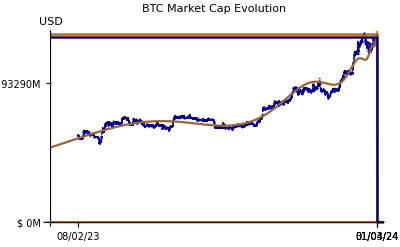

```mathematica
marketCapPrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Market Cap Evolution",PlotRange->{{0,maxTc},{0,Exp[bestM]}}, Ticks->{ticksH,ticksVM},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestM+1],UnitStep[ti-highCItc]Exp[bestM+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIM],UnitStep[bestTc-ti]Exp[bestM],UnitStep[lastScaledTc-ti]Exp[lastScaledM]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"BTC_MarketCapPrediction-"<>lastPriceDate<>".png",marketCapPrediction]
```

/Users/mauro/Projects/Bitcoin/BTC_MarketCapPrediction-2024-05-03.png

```mathematica
mToMarketCap[m_]:= latestMarketCap/Exp[lastScaledM] Exp[m]
```

```mathematica
lowCIMarketCap=mToMarketCap[lowCIM]
```

124403.

```mathematica
bestMarketCap=mToMarketCap[bestM]
```

125910.

```mathematica
(* The price is the ratio of the market cap (in Millions USD) to the (predicted) supply at the date: *)
mToPrice[m_, date_]:=mToMarketCap[m]10^7/supplyFunction[UnixTime[date]]
```

```mathematica
tcToDate[tc_]:= DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]tc/lastScaledTc]
```

```mathematica
(* Check: *)
lastPrice=mToPrice[lastScaledM,tcToDate[lastScaledTc]]
```

62967.8

```mathematica
lowCIPrice=mToPrice[lowCIM, tcToDate[lowCItc]]
```

63247.4

```mathematica
bestPrice=mToPrice[bestM, tcToDate[bestTc]]
```

64012.

```mathematica
(* Plot predicted price evolution (USD) :*)
ticksVPrice[min_,max_]:=Table[{i,"$"<>ToString[IntegerPart[i]]},{i,min, max,25000}]
```

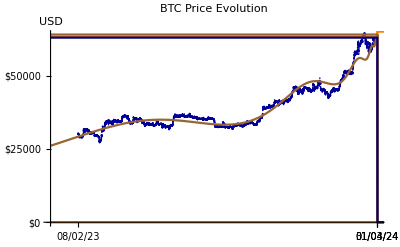

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], mToPrice[#[[2]], tcToDate[#[[1]]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Price Evolution",PlotRange->{{0,maxTc},{0,bestPrice}}, Ticks->{ticksH,ticksVPrice},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[mToPrice[lpplsModel/.fit, tcToDate[ti]]],UnitStep[ti-lowCItc](bestPrice+1000),UnitStep[ti-highCItc](bestPrice+1000)/.fit, UnitStep[lowCItc-ti]lowCIPrice,UnitStep[bestTc-ti]bestPrice,UnitStep[lastScaledTc-ti]lastPrice}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_PricePrediction-2024-05-03.png